```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
Quantity[3,"Minutes"]
```

3 min

```mathematica
FileSize[$CommandLine[[1]]]
```

48.304 kB

## update

```mathematica
PacletUninstall["CodeParser"]
```

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/codeparser/build/paclet/CodeParser-999.paclet"]
```

PacletObject[CodeParser,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/codeparser/build/paclet/CodeParser"];
```

```mathematica
FindFile["CodeParser`"]
```

/Users/brenton/development/stash/COD/ast/build/paclet/AST/Kernel/AST.wl

```mathematica
PacletUpdate["CodeParser","UpdateSites"->True]
```

PacletObject[AST,0.15,<>]

## alphasource Git error

git remote prune origin

git gc --prune=now

git remote prune origin

## build with gcc for -Weffc++ warnings

mkdir build-gcc
cd build-gcc
cmake -DWOLFRAMKERNEL=/Applications/Mathematica110.app/Contents/MacOS/WolframKernel -DCMAKE_CXX_COMPILER=/usr/local/bin/g++-8 -DCMAKE_C_COMPILER=/usr/local/bin/gcc-8 ..
cmake --build . --target paclet

## build with a compilation command database for clang-tidy

mkdir build-clang-tidy
cd build-clang-tidy
cmake -DCMAKE_EXPORT_COMPILE_COMMANDS=ON ..

generates a compile_commands.json in current directory that clang-tidy uses

clang-tidy ByteDecoder.cpp
clang-tidy ByteEncoder.cpp
...

## build for afl fuzzing

Building AFL for the kernel

# build llvm

cd llvm-development
mkdir llvm8
cd llvm8
git clone https://github.com/llvm/llvm-project.git

cd llvm-project/

git fetch
git checkout release/8.x

mkdir build

cd build

cmake -DLLVM_BUILD_LLVM_DYLIB=ON -DLLVM_LINK_LLVM_DYLIB=ON -DLLVM_ENABLE_RTTI=ON -DCMAKE_OSX_DEPLOYMENT_TARGET=10.10 -DCMAKE_INSTALL_PREFIX=install -DLLVM_ENABLE_PROJECTS="clang;libcxx;libcxxabi;lld;compiler-rt" -G "Ninja" ../llvm

ninja
ninja install

# build afl

export CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

cd afl-2.5b
CFLAGS="-mmacosx-version-min=10.10" make

cd llvm-mode
export LLVM_CONFIG=/Users/brenton/development/llvm-development/llvm801/llvm-project/build/install/bin/llvm-config
CFLAGS="-mmacosx-version-min=10.10" make

# build ast

export AFL_CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export AFL_CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

mkdir build-afl
cd build-afl
cmake -DCMAKE_INSTALL_PREFIX=install -DBUILD_EXE=ON -DCMAKE_BUILD_TYPE=Debug -DCMAKE_C_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast  -DCMAKE_CXX_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast++ ..

cmake --build . --target ast-exe

/Users/brenton/development/other-development/afl-2.52b/afl-fuzz -i /Users/brenton/development/stash/COD/ast/Tests/files/small -o afl_out/ -x ../Tests/wl.dict cpp/src/exe/ast -n -file @@

## build for GCOV

mkdir build-gcc
cd build-gcc

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o API.o -c ../cpp/src/lib/API.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteBuffer.o -c ../cpp/src/lib/ByteBuffer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteDecoder.o -c ../cpp/src/lib/ByteDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteEncoder.o -c ../cpp/src/lib/ByteEncoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterDecoder.o -c ../cpp/src/lib/CharacterDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Node.o -c ../cpp/src/lib/Node.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parselet.o -c ../cpp/src/lib/Parselet.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parser.o -c ../cpp/src/lib/Parser.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Source.o -c ../cpp/src/lib/Source.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o SemiSemiParselet.o -c ../cpp/src/lib/SemiSemiParselet.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Tokenizer.o -c ../cpp/src/lib/Tokenizer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Utils.o -c ../cpp/src/lib/Utils.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o WLCharacter.o -c ../cpp/src/lib/WLCharacter.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterMaps.o -c ../build/generated/cpp/src/lib/CharacterMaps.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Token.o -c ../cpp/src/lib/Token.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CodePoint.o -c ../build/generated/cpp/src/lib/CodePoint.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Symbol.o -c ../build/generated/cpp/src/lib/Symbol.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o TokenEnum.o -c ../build/generated/cpp/src/lib/TokenEnum.cpp


/usr/local/bin/g++-8 --coverage -dynamiclib API.o ByteBuffer.o ByteDecoder.o ByteEncoder.o CharacterDecoder.o Node.o Parselet.o Parser.o SemiSemiParselet.o Source.o Tokenizer.o Utils.o WLCharacter.o CharacterMaps.o Token.o CodePoint.o Symbol.o TokenEnum.o -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -framework mathlink -o AST.dylib


/usr/local/bin/g++-8  -I ../cpp/include -I ../build/generated/cpp/include -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C  --coverage   -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -std=gnu++11 -o main.o -c ../cpp/src/exe/main.cpp


mkdir Frameworks
cd Frameworks
cp -r /Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/mathlink.framework .
cd ..

mkdir exe
cd exe
/usr/local/bin/g++-8  --coverage ../main.o  -o ast -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions ../AST.dylib -framework mathlink
cd ..
 
 
exe/ast -file ../Tests/files/carriagereturn.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0003.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-contexts.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-specialchararacters.txt  > /dev/null
exe/ast -file ../Tests/files/linearsyntax.wl > /dev/null
exe/ast -file ../Tests/files/comments.wl > /dev/null
exe/ast -file ../Tests/files/inputs-characternameoperations.txt > /dev/null
exe/ast -file ../Tests/files/inputs-integers.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/package.wl > /dev/null
exe/ast -file ../Tests/files/crash.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternames.txt > /dev/null
exe/ast -file ../Tests/files/inputs-nestedsymbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic2.txt > /dev/null
exe/ast -file ../Tests/files/sample.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0001.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternamestrings.txt > /dev/null
exe/ast -file ../Tests/files/inputs-random.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic3.txt > /dev/null
exe/ast -file ../Tests/files/shebangwarning.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0002.txt > /dev/null
exe/ast -file ../Tests/files/inputs-comments.txt > /dev/null
exe/ast -file ../Tests/files/inputs-reals.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic4.txt > /dev/null
exe/ast -file ../Tests/files/strange.wl > /dev/null


/usr/local/bin/gcov-8 API.cpp
/usr/local/bin/gcov-8 ByteBuffer.cpp
/usr/local/bin/gcov-8 ByteDecoder.cpp
/usr/local/bin/gcov-8 ByteEncoder.cpp
/usr/local/bin/gcov-8 CharacterDecoder.cpp
/usr/local/bin/gcov-8 Node.cpp
/usr/local/bin/gcov-8 Parselet.cpp
/usr/local/bin/gcov-8 Parser.cpp
/usr/local/bin/gcov-8 SemiSemiParselet.cpp
/usr/local/bin/gcov-8 SyntaxIssue.cpp
/usr/local/bin/gcov-8 Tokenizer.cpp
/usr/local/bin/gcov-8 Utils.cpp
/usr/local/bin/gcov-8 WLCharacter.cpp
/usr/local/bin/gcov-8 CharacterMaps.cpp
/usr/local/bin/gcov-8 Token.cpp
/usr/local/bin/gcov-8 TokenEnum.cpp
/usr/local/bin/gcov-8 CodePoint.cpp
/usr/local/bin/gcov-8 Symbol.cpp

## build for Leak Sanitizing

brenton2maclap:build-leak brenton$ /Users/brenton/development/llvm-development/llvm900/llvm-project/build/install/bin/clang++ -I ../cpp/include -I generated/cpp/include -I /Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I /Applications/Mathematica110.app/Contents/SystemFiles/IncludeFiles/C -fsanitize=address -g -std=c++11 -L/Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/ -lMLi4 -framework Foundation ../cpp/src/exe/main.cpp ../cpp/src/lib/API.cpp ../cpp/src/lib/ByteDecoder.cpp ../cpp/src/lib/ByteEncoder.cpp ../cpp/src/lib/CharacterDecoder.cpp ../cpp/src/lib/Node.cpp ../cpp/src/lib/Parselet.cpp ../cpp/src/lib/SemiSemiParselet.cpp ../cpp/src/lib/Source.cpp ../cpp/src/lib/SourceManager.cpp ../cpp/src/lib/Token.cpp ../cpp/src/lib/Tokenizer.cpp ../cpp/src/lib/Utils.cpp generated/cpp/src/lib/CodePoint.cpp generated/cpp/src/lib/CharacterMaps.cpp generated/cpp/src/lib/Symbol.cpp ../cpp/src/lib/Parser.cpp ../cpp/src/lib/WLCharacter.cpp generated/cpp/src/lib/TokenEnum.cpp ; ASAN_OPTIONS=detect_leaks=1 ./a.out

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Needs["CodeParser`"]
```

```mathematica
CodeParser`Private`$Debug=xTrue;
```

```mathematica
xSetSystemOptions["StrictLexicalScoping"->False];
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
PrependTo[$Path,"/Users/brenton/development/stash/COD/codeparser/Tests/CodeParserTestUtils/"];
```

```mathematica
Needs["CodeParserTestUtils`"]
```

## Init: shims

```mathematica
Needs["AST`"]
```

```mathematica
AST`Shims`Private`setupStackShim[]
```

## Init: setup LongNames

```mathematica
Needs["AST`"]
```

```mathematica
AST`Library`SetupLongNames[]
```

## MExprParser

ANTLR parser history:
https://cvs-master.wolfram.com/viewvc/RD_HTML/TWJ/LocalWork/Parsers/ExprAST/?view=query&branch=&branch_match=exact&dir=&file=&file_match=exact&who=&who_match=exact&comment=&comment_match=exact&querysort=date&hours=2&date=all&mindate=&maxdate=&limit_changes=

https://stash.wolfram.com/projects/JAVA/repos/mexprparser/commits

## other parsers

https://github.com/halirutan/Mathematica-IntelliJ-Plugin

https://github.com/mathics/Mathics/tree/master/mathics/core/parser

https://github.com/rljacobson/FoxySheep

https://atom.io/packages/linter-mathematica

https://github.com/halirutan/Wolfram-Language-Parser

https://www.robertjacobson.dev/defining-the-wolfram-language-part-1-finding-operators

https://gitlab.com/cznic/wl

## test a single file

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
file="/Users/brenton/development/stash/COD/ast/build/test.m";
```

```mathematica
file="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m";
```

```mathematica
Head[file]
```

String

```mathematica
FileByteCount[file]
```

9

```mathematica
actualCST=ConcreteParseFile[file,HoldNode[Hold,#[[1]],<||>]&];
```

```mathematica
If[!FreeQ[actualCST,_SyntaxErrorNode],
Print["has errors"]
]
```

```mathematica
actualAgg=AST`Abstract`Aggregate[actualCST];
```

```mathematica
tryString=ToInputFormString[actualAgg];
If[!StringQ[tryString],
Print["tryString is not a String"];
]
```

```mathematica
If[!FreeQ[actualAgg,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
(text=FromCharacterCode[Import[file,"Byte"],"UTF8"])//FullForm;
```

```mathematica
If[!FreeQ[actualCST,LeafNode[Symbol,"Package",_]],
text=StringReplace[text,"Package"->"PackageXXX"];
]
```

```mathematica
expected=DeleteCases[ToExpression[text,InputForm,Hold],Null];//AbsoluteTiming
```

{0.00001,Null}

```mathematica
actual===expected
```

True

```mathematica
(* Abstract *)
actualAST=AST`Abstract`Abstract[actualAgg];
```

```mathematica
tryString=ToFullFormString[actualAST];
If[!StringQ[tryString],
Print[tryString];
Quit[]
]
```

```mathematica
If[!FreeQ[actualAST,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
actual===expected
```

True

```mathematica
expected=$LastFailedExpected;
```

```mathematica
actual=$LastFailedActual;
```

```mathematica
Length[expected]
```

5

```mathematica
Length[actual]
```

5

```mathematica
Position[Table[Extract[expected,{i},Hold]===Extract[actual,{i},Hold],{i,1,Min[Length[actual],Length[expected]]}],False]
```

{{2},{4}}

```mathematica
spec={2};
a=Extract[expected,spec,Hold]//FullForm
b=Extract[actual,spec,Hold]//FullForm
a===b
```

Hold[CompoundExpression[Begin["`Private`"],Null]]

Hold[Begin["`Private`"]]

False

```mathematica
Do[
Pause[0.01];
spec={66,1,2,2,i};
a=Extract[expected,spec,Hold];
b=Extract[actual,spec,Hold];
If[a=!=b,Print[i];Break[]]
,
{i,1,10000}
]
```

6

```mathematica
FilePrint[file]
```

PacletManager`Package`getPacletWithProgress["AstronomyConvenienceFunctions"];



Get["AstronomyConvenienceFunctions`"]

## test all files

```mathematica
prefix:=stash<>"QA/";
prefix:=protos;
prefix:="/Users/brenton/development/github-development/";
prefix=installation;
names1:=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"(*"*.nb"*),prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"|"*.wls",prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];

(*
Directory, not a file
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];

(*
weird
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"system/InputOutput/Get/corruptedprefs.m"]];
names=Complement[names,toDelete];
```

5784

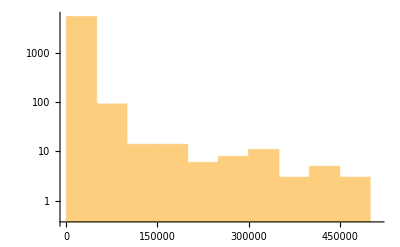

```mathematica
Length[names]
Histogram[FileByteCount/@names,100,ScalingFunctions->"Log"]
```

```mathematica
$ProcessID
```

7054

```mathematica
$DebugLoop=xTrue;
$visuals=xTrue;
```

```mathematica
CodeParserTestUtils`Private`$DebugTopLevelExpressions=xTrue;
```

```mathematica
$minSizeLimit=0.00*^6;
$maxSizeLimit=5.00*^6;
```

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Parsing ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
If[$visuals,
Print["Current file bytes/s: ",Dynamic[bytesPerSecond]]
];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete",Dynamic[CodeParser`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[CodeParser`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate",Dynamic[CodeParser`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract",Dynamic[CodeParser`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AbstractParseProgress],{0,100}]},
{"","",Dynamic[PieChart[{CodeParser`Library`$ConcreteParseTime,CodeParser`Abstract`$AggregateParseTime,CodeParser`Abstract`$AbstractParseTime},ImageSize->Tiny,ChartLegends->{"concrete","aggregate","abstract"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

CodeParser`Library`$ConcreteParseProgress=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseProgress=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseProgress=Quantity[0,"Seconds"];
CodeParser`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
bytesPerSecond=0;
res=CodeParserTestUtils`parseTest[#,x,"FileNamePrefixPattern"->prefix,"FileSizeLimit"->{$minSizeLimit,$maxSizeLimit}];
(*implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
If[res=!=ok,
If[$visuals,
bytesPerSecond=FileSize[file]/(CodeParser`Library`$ConcreteParseTime);
Pause[2.0];
];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

Parsing 5784 files

Current file:

Current file size:

Current index:

overall

100 /Applications/Mathematica121-6670671.app/Contents/AddOns/Applications/EntityFramework/Kernel/Registry.m

200 /Applications/Mathematica121-6670671.app/Contents/AddOns/Applications/QuantityUnits/Kernel/Typesetting.m

300 /Applications/Mathematica121-6670671.app/Contents/AddOns/Packages/GraphUtilities/Kernel/init.m

400 /Applications/Mathematica121-6670671.app/Contents/AddOns/Packages/GUIKit/src/mathematica/Kernel/GUIRuntime.m

500 /Applications/Mathematica121-6670671.app/Contents/AddOns/Packages/WorldPlot/WorldData.m

600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/CharacterEncodings/WindowsGreek.m

700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/BellB.m

800 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/ChiDistribution.m

900 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Curl.m

1000 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/EdgeDelete.m

1100 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/FindSequenceFunction.m

1200 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/GraphPlot3D.m

1300 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Inpaint.m

1400 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Laplace.m

1500 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/MathieuCharacteristicB.m

1600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/NRoots.m

1700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/PolyGamma.m

1800 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Record.m

1900 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/SiegelTheta.m

2000 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/SubscriptBox.m

2100 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/TrimmedMean.m

2200 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/JapaneseOptionValues.m

2300 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/DateRange.m

2400 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/Graphics.m

2500 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/ListDensityPlot.m

2600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/ParametricNDSolveValue.m

2700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/SmoothHistogram.m

index: 2796 SystemFiles/Components/AutoCompletionData/Main/shortToLongForm.m

index: 2796 Messages while processing expected input (possibly from previous files):

{} (Most likely Syntax Messages, but Syntax Messages don't show up in $MessageList: bug 210020)

index: 2796 SystemFiles/Components/AutoCompletionData/Main/shortToLongForm.m

index: 2796 Messages while processing actual input (possibly from previous files):

{} (Most likely Syntax Messages, but Syntax Messages don't show up in $MessageList: bug 210020)

index: 2796 SystemFiles/Components/AutoCompletionData/Main/shortToLongForm.m

index: 2796 Messages while processing actual input (possibly from previous files):

{} (Most likely Syntax Messages, but Syntax Messages don't show up in $MessageList: bug 210020)

index: 2796 SystemFiles/Components/AutoCompletionData/Main/shortToLongForm.m

index: 2796 Messages while processing actual input (possibly from previous files):

{} (Most likely Syntax Messages, but Syntax Messages don't show up in $MessageList: bug 210020)

2800 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/AutoCompletionData/Main/Vietnamese.m

index: 2807 SystemFiles/Components/Blockchain/Ark.m

index: 2807 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2808 SystemFiles/Components/Blockchain/Bitcoin.m

index: 2808 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2810 SystemFiles/Components/Blockchain/Ethereum.m

index: 2810 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2811 SystemFiles/Components/Blockchain/Main.m

index: 2811 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2813 SystemFiles/Components/Blockchain/SmartContracts.m

index: 2813 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2814 SystemFiles/Components/Blockchain/Token.m

index: 2814 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2815 SystemFiles/Components/Blockchain/UtilitiesARK.m

index: 2815 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2816 SystemFiles/Components/Blockchain/UtilitiesBTC.m

index: 2816 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2817 SystemFiles/Components/Blockchain/UtilitiesETH.m

index: 2817 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2818 SystemFiles/Components/Blockchain/Utilities.m

index: 2818 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2819 SystemFiles/Components/Blockchain/Wolfram.m

index: 2819 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2820 SystemFiles/Components/CacheManager/Flushing.m

index: 2820 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2822 SystemFiles/Components/CacheManager/Manager.m

index: 2822 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2824 SystemFiles/Components/CacheManager/SpillCache.m

index: 2824 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 2825 SystemFiles/Components/CacheManager/Utils.m

index: 2825 Package symbol detected (bug 347012); rewriting Package→PackageXXX

2900 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Chemistry/Kernel/ToEntity.wl

3000 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/AST/Semantics/DeBruijnIndex.m

3100 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/CompileResources/TypePredictionManual/Inverse.wl

3200 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/Core/Analysis/Loop/Loop.m

3300 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/Core/IR/IR.m

3400 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/Core/PassManager/PassInformation.m

3500 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Compile/TypeSystem/Bootstrap/Hash/Numeric.m

3600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/CrossRef/PacletInfo.m

index: 3602 SystemFiles/Components/Cryptography/DeterministicK.m

index: 3602 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3603 SystemFiles/Components/Cryptography/EllipticCurveKeyObjects.m

index: 3603 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3604 SystemFiles/Components/Cryptography/EllipticCurves.m

index: 3604 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3605 SystemFiles/Components/Cryptography/EncryptDecryptFile.m

index: 3605 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3606 SystemFiles/Components/Cryptography/EncryptDecrypt.m

index: 3606 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3607 SystemFiles/Components/Cryptography/EncryptedObject.m

index: 3607 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3608 SystemFiles/Components/Cryptography/FileSignatures.m

index: 3608 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3609 SystemFiles/Components/Cryptography/GenerateAsymmetricKeyPair.m

index: 3609 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3610 SystemFiles/Components/Cryptography/GenerateDerivedKey.m

index: 3610 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3611 SystemFiles/Components/Cryptography/GenerateSymmetricKey.m

index: 3611 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3612 SystemFiles/Components/Cryptography/OpenSSLLink.m

index: 3612 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3614 SystemFiles/Components/Cryptography/PrivateKey.m

index: 3614 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3615 SystemFiles/Components/Cryptography/PublicKey.m

index: 3615 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3616 SystemFiles/Components/Cryptography/RSAKeyObjects.m

index: 3616 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3617 SystemFiles/Components/Cryptography/Signatures.m

index: 3617 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3618 SystemFiles/Components/Cryptography/summaryBoxes.m

index: 3618 Package symbol detected (bug 347012); rewriting Package→PackageXXX

3700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/DataStructure/Source/FixedArray/Loader.m

3800 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Flickr/Kernel/load.m

3900 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/GraphStore/Kernel/Formats/TriG/Converter.wl

index: 3981 SystemFiles/Components/HTTPHandling/Main.m

index: 3981 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3983 SystemFiles/Components/Iconize/Constants.m

index: 3983 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3984 SystemFiles/Components/Iconize/HelperFunctions.m

index: 3984 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3987 SystemFiles/Components/Iconize/NotebookRasterize.m

index: 3987 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3990 SystemFiles/Components/Iconize/ToFormattedIcon.m

index: 3990 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 3991 SystemFiles/Components/Iconize/ToRawIcon.m

index: 3991 Package symbol detected (bug 347012); rewriting Package→PackageXXX

4000 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/IntegratedServices/Kernel/IntegratedServicesManagment.m

index: 4087 SystemFiles/Components/Macros/ArgumentCount.m

index: 4087 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4088 SystemFiles/Components/Macros/Evaluation.m

index: 4088 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4090 SystemFiles/Components/Macros/Macros.m

index: 4090 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4092 SystemFiles/Components/Macros/Options.m

index: 4092 Package symbol detected (bug 347012); rewriting Package→PackageXXX

4100 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/MicrocontrollerKit/Kernel/Atmel8.m

index: 4168 SystemFiles/Components/NumericArrayUtilities/Kernel/ArrayMerge.m

index: 4168 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4169 SystemFiles/Components/NumericArrayUtilities/Kernel/BarnesHutTSNE.m

index: 4169 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4170 SystemFiles/Components/NumericArrayUtilities/Kernel/BinarySearch.m

index: 4170 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4171 SystemFiles/Components/NumericArrayUtilities/Kernel/BPE.m

index: 4171 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4172 SystemFiles/Components/NumericArrayUtilities/Kernel/Common.m

index: 4172 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4173 SystemFiles/Components/NumericArrayUtilities/Kernel/CTCDecode.m

index: 4173 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4174 SystemFiles/Components/NumericArrayUtilities/Kernel/DecisionTree/DecisionTreeClassifyPredict.m

index: 4174 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4175 SystemFiles/Components/NumericArrayUtilities/Kernel/DecisionTree/DecisionTreeCommon.m

index: 4175 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4176 SystemFiles/Components/NumericArrayUtilities/Kernel/DecisionTree/DecisionTreeLearnDistribution.m

index: 4176 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4177 SystemFiles/Components/NumericArrayUtilities/Kernel/DistanceMatrix.m

index: 4177 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4178 SystemFiles/Components/NumericArrayUtilities/Kernel/GeneralUtils.m

index: 4178 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4179 SystemFiles/Components/NumericArrayUtilities/Kernel/HadamardReduce.m

index: 4179 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4181 SystemFiles/Components/NumericArrayUtilities/Kernel/NADE.m

index: 4181 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4182 SystemFiles/Components/NumericArrayUtilities/Kernel/SetMantissaPrecision.m

index: 4182 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4183 SystemFiles/Components/NumericArrayUtilities/Kernel/Sorting.m

index: 4183 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4185 SystemFiles/Components/ONNXUtilities/Kernel/ACommon.m

index: 4185 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4186 SystemFiles/Components/ONNXUtilities/Kernel/Importer.m

index: 4186 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4187 SystemFiles/Components/ONNXUtilities/Kernel/init.m

index: 4187 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4188 SystemFiles/Components/ONNXUtilities/Kernel/LayerImporter.m

index: 4188 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4189 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Abs.m

index: 4189 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4190 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Acosh.m

index: 4190 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4191 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Acos.m

index: 4191 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4192 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Add.m

index: 4192 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4193 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Asinh.m

index: 4193 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4194 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Asin.m

index: 4194 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4195 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Atanh.m

index: 4195 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4196 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Atan.m

index: 4196 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4197 SystemFiles/Components/ONNXUtilities/Kernel/Layers/AveragePool.m

index: 4197 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4198 SystemFiles/Components/ONNXUtilities/Kernel/Layers/BatchNormalization.m

index: 4198 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4199 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Ceil.m

index: 4199 Package symbol detected (bug 347012); rewriting Package→PackageXXX

4200 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/ONNXUtilities/Kernel/Layers/Clip.m

index: 4200 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Clip.m

index: 4200 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4201 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Concat.m

index: 4201 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4202 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Constant.m

index: 4202 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4203 SystemFiles/Components/ONNXUtilities/Kernel/Layers/ConstantOfShape.m

index: 4203 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4204 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Conv.m

index: 4204 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4205 SystemFiles/Components/ONNXUtilities/Kernel/Layers/ConvTranspose.m

index: 4205 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4206 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Cosh.m

index: 4206 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4207 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Cos.m

index: 4207 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4208 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Div.m

index: 4208 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4209 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Dropout.m

index: 4209 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4210 SystemFiles/Components/ONNXUtilities/Kernel/Layers/ELU.m

index: 4210 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4211 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Erf.m

index: 4211 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4212 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Exp.m

index: 4212 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4213 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Flatten.m

index: 4213 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4214 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Floor.m

index: 4214 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4215 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Gather.m

index: 4215 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4216 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Gemm.m

index: 4216 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4217 SystemFiles/Components/ONNXUtilities/Kernel/Layers/GlobalAveragePool.m

index: 4217 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4218 SystemFiles/Components/ONNXUtilities/Kernel/Layers/GlobalMaxPool.m

index: 4218 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4220 SystemFiles/Components/ONNXUtilities/Kernel/Layers/HardSigmoid.m

index: 4220 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4221 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Identity.m

index: 4221 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4222 SystemFiles/Components/ONNXUtilities/Kernel/Layers/InstanceNormalization.m

index: 4222 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4223 SystemFiles/Components/ONNXUtilities/Kernel/Layers/LayerUtils.m

index: 4223 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4224 SystemFiles/Components/ONNXUtilities/Kernel/Layers/LeakyRelu.m

index: 4224 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4225 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Log.m

index: 4225 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4226 SystemFiles/Components/ONNXUtilities/Kernel/Layers/LogSoftmax.m

index: 4226 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4227 SystemFiles/Components/ONNXUtilities/Kernel/Layers/LRN.m

index: 4227 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4229 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Max.m

index: 4229 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4230 SystemFiles/Components/ONNXUtilities/Kernel/Layers/MaxPool.m

index: 4230 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4231 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Mean.m

index: 4231 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4232 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Min.m

index: 4232 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4233 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Mul.m

index: 4233 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4234 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Neg.m

index: 4234 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4235 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Pow.m

index: 4235 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4236 SystemFiles/Components/ONNXUtilities/Kernel/Layers/PReLU.m

index: 4236 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4237 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Reciprocal.m

index: 4237 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4238 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Relu.m

index: 4238 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4239 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Reshape.m

index: 4239 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4241 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Round.m

index: 4241 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4242 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Selu.m

index: 4242 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4243 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Shrink.m

index: 4243 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4244 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sigmoid.m

index: 4244 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4245 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sign.m

index: 4245 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4246 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sinh.m

index: 4246 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4247 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sin.m

index: 4247 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4248 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Softmax.m

index: 4248 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4249 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Softplus.m

index: 4249 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4250 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Softsign.m

index: 4250 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4251 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sqrt.m

index: 4251 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4252 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sub.m

index: 4252 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4253 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sum.m

index: 4253 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4254 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Tanh.m

index: 4254 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4255 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Tan.m

index: 4255 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4256 SystemFiles/Components/ONNXUtilities/Kernel/Layers/ThresholdedRelu.m

index: 4256 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4257 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Transpose.m

index: 4257 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4258 SystemFiles/Components/ONNXUtilities/Kernel/Layers/Unsqueeze.m

index: 4258 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4259 SystemFiles/Components/ONNXUtilities/Kernel/Utils.m

index: 4259 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4262 SystemFiles/Components/OpenLibrary/Kernel/OpenLibraryFunctions.m

index: 4262 Failure[…]

index: 4293 SystemFiles/Components/Pushbullet/Kernel/PushbulletAPIFunctions.m

index: 4293 Failure[…]

4300 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/Reddit/Kernel/Reddit.m

index: 4302 SystemFiles/Components/ReinforcementLearning/Kernel/Common.m

index: 4302 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4303 SystemFiles/Components/ReinforcementLearning/Kernel/Environments/OpenAIGym.m

index: 4303 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4304 SystemFiles/Components/ReinforcementLearning/Kernel/Environments/SimulatedCartPole.m

index: 4304 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4305 SystemFiles/Components/ReinforcementLearning/Kernel/Environments/Testing/StateHistoryTests.m

index: 4305 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4306 SystemFiles/Components/ReinforcementLearning/Kernel/Environments/Testing/Testing.m

index: 4306 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4307 SystemFiles/Components/ReinforcementLearning/Kernel/init.m

index: 4307 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4308 SystemFiles/Components/ReinforcementLearning/Kernel/Solvers/AugmentedRandomSearch.m

index: 4308 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4309 SystemFiles/Components/ReinforcementLearning/Kernel/Solvers/PPO/PPOLossFunction.m

index: 4309 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4310 SystemFiles/Components/ReinforcementLearning/Kernel/Utilities/AdvantageEstimators.m

index: 4310 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4311 SystemFiles/Components/ReinforcementLearning/Kernel/Utilities/EnvironmentRunners.m

index: 4311 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4312 SystemFiles/Components/ReinforcementLearning/Kernel/Utilities/GeneralUtils.m

index: 4312 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4313 SystemFiles/Components/ReinforcementLearning/Kernel/Utilities/PolicyNets.m

index: 4313 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4314 SystemFiles/Components/ReinforcementLearning/Kernel/Utilities/Scoring.m

index: 4314 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4356 SystemFiles/Components/ResourceSystemClient/Kernel/Autocomplete.m

index: 4356 Messages while processing expected input (possibly from previous files):

{$ResourceSystemBase::shdw}

index: 4356 There were General::shdw messages; rerunning

4400 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/ResourceSystemClient/Kernel/Submissions.m

index: 4425 SystemFiles/Components/RobotTools/Kernel/InstallRobotTools.m

index: 4425 Messages while processing expected input (possibly from previous files):

{getProperty::shdw}

index: 4425 There were General::shdw messages; rerunning

4500 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/SpellingData/Kernel/SpellingDataLoader.m

4600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/TypeFramework/TypeObjects/TypeVariable.m

index: 4661 SystemFiles/Components/WolframClientForPython/wolframclient/tests/data/allbytes.wl

index: 4661 Messages while processing expected input (possibly from previous files):

{$CharacterEncoding::utf8,$CharacterEncoding::utf8,$CharacterEncoding::utf8,General::stop}

index: 4661 SystemFiles/Components/WolframClientForPython/wolframclient/tests/data/allbytes.wl

index: 4661 Failure[…]

4700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSMLink/Results/SimulationData.m

index: 4715 SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSM/TextResources/English/Messages.m

index: 4715 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4717 SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSM/TextResources/Japanese/Messages.m

index: 4717 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 4726 SystemFiles/Components/Yelp/Kernel/YelpFunctions.m

index: 4726 Failure[…]

4800 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Formats/CDXML/Import.m

4900 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Formats/ICC/Import.m

5000 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Formats/OFF/Export.m

5100 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Formats/Table/Import.m

5200 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/ArchiveTools/Kernel/ArchiveTools.m

index: 5225 SystemFiles/Links/AWSLink/Kernel/AWS.m

index: 5225 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5226 SystemFiles/Links/AWSLink/Kernel/Common.m

index: 5226 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5227 SystemFiles/Links/AWSLink/Kernel/EC2.m

index: 5227 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5228 SystemFiles/Links/AWSLink/Kernel/EC2Templates.m

index: 5228 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5229 SystemFiles/Links/AWSLink/Kernel/ErrorHandling.m

index: 5229 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5267 SystemFiles/Links/CloudObject/Kernel/Permissions.m

index: 5267 Messages while processing expected input (possibly from previous files):

{ApplicationIdentificationKey::shdw}

index: 5267 There were General::shdw messages; rerunning

index: 5291 SystemFiles/Links/DAALLink/Kernel/common.m

index: 5291 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5292 SystemFiles/Links/DAALLink/Kernel/ExMaxGMModel.m

index: 5292 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5293 SystemFiles/Links/DAALLink/Kernel/GBT.m

index: 5293 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5294 SystemFiles/Links/DAALLink/Kernel/init.m

index: 5294 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5295 SystemFiles/Links/DAALLink/Kernel/LogisticRegression.m

index: 5295 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5296 SystemFiles/Links/DAALLink/Kernel/RandomForest.m

index: 5296 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5297 SystemFiles/Links/DAALLink/Kernel/SVM.m

index: 5297 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5298 SystemFiles/Links/DAALLink/Kernel/table.m

index: 5298 Package symbol detected (bug 347012); rewriting Package→PackageXXX

5300 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/DatabaseLink/DatabaseExamples.m

index: 5348 SystemFiles/Links/Databases/Databases/Common/Common.m

index: 5348 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5349 SystemFiles/Links/Databases/Databases/Common/Errors.m

index: 5349 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5350 SystemFiles/Links/Databases/Databases/Common/Icons.m

index: 5350 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5351 SystemFiles/Links/Databases/Databases/Common/ImmutableObject.m

index: 5351 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5353 SystemFiles/Links/Databases/Databases/Common/MessageHandling.m

index: 5353 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5354 SystemFiles/Links/Databases/Databases/Common/Proxy.m

index: 5354 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5355 SystemFiles/Links/Databases/Databases/Common/Resource.m

index: 5355 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5356 SystemFiles/Links/Databases/Databases/Common/StackTraces.m

index: 5356 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5357 SystemFiles/Links/Databases/Databases/Database/Boxes.m

index: 5357 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5358 SystemFiles/Links/Databases/Databases/Database/Compiler/aTypeSignatures.m

index: 5358 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5359 SystemFiles/Links/Databases/Databases/Database/Compiler/Checks.m

index: 5359 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5360 SystemFiles/Links/Databases/Databases/Database/Compiler/DatabaseFunction.m

index: 5360 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5361 SystemFiles/Links/Databases/Databases/Database/Compiler/DBQueryCompiler.m

index: 5361 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5362 SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m

index: 5362 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5363 SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionProcessor.m

index: 5363 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5364 SystemFiles/Links/Databases/Databases/Database/Compiler/Inference.m

index: 5364 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5365 SystemFiles/Links/Databases/Databases/Database/Compiler/Interface.m

index: 5365 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5366 SystemFiles/Links/Databases/Databases/Database/Compiler/SignaturesRegistry.m

index: 5366 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5367 SystemFiles/Links/Databases/Databases/Database/Compiler/SyntheticFields.m

index: 5367 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5368 SystemFiles/Links/Databases/Databases/Database/DatabaseStore.m

index: 5368 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5369 SystemFiles/Links/Databases/Databases/Database/Execution.m

index: 5369 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5371 SystemFiles/Links/Databases/Databases/Database/Operation.m

index: 5371 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5372 SystemFiles/Links/Databases/Databases/Database/Predicates.m

index: 5372 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5373 SystemFiles/Links/Databases/Databases/Database/Relations.m

index: 5373 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5374 SystemFiles/Links/Databases/Databases/Database/SerializeData.m

index: 5374 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5375 SystemFiles/Links/Databases/Databases/Entity/Boxes.m

index: 5375 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5376 SystemFiles/Links/Databases/Databases/Entity/DBFieldConversion.m

index: 5376 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5377 SystemFiles/Links/Databases/Databases/Entity/EntityFunction.m

index: 5377 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5378 SystemFiles/Links/Databases/Databases/Entity/EntityRelations.m

index: 5378 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5379 SystemFiles/Links/Databases/Databases/Entity/EntityStore.m

index: 5379 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5380 SystemFiles/Links/Databases/Databases/Entity/EntityValue.m

index: 5380 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5381 SystemFiles/Links/Databases/Databases/Entity/Errors.m

index: 5381 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5383 SystemFiles/Links/Databases/Databases/Entity/ToDatabaseQuery.m

index: 5383 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5384 SystemFiles/Links/Databases/Databases/Impl.m

index: 5384 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5385 SystemFiles/Links/Databases/Databases/Init.m

index: 5385 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5386 SystemFiles/Links/Databases/Databases/Interface.m

index: 5386 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5388 SystemFiles/Links/Databases/Databases/Messages.m

index: 5388 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5390 SystemFiles/Links/Databases/Databases/Python/Python.m

index: 5390 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5391 SystemFiles/Links/Databases/Databases/Python/Serialization.m

index: 5391 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5392 SystemFiles/Links/Databases/Databases/Schema/Boxes.m

index: 5392 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5393 SystemFiles/Links/Databases/Databases/Schema/Connection.m

index: 5393 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5394 SystemFiles/Links/Databases/Databases/Schema/DBTypeContainsQ.m

index: 5394 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5395 SystemFiles/Links/Databases/Databases/Schema/DBType.m

index: 5395 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5396 SystemFiles/Links/Databases/Databases/Schema/Inspection.m

index: 5396 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5398 SystemFiles/Links/Databases/Databases/Schema/Patterns.m

index: 5398 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5399 SystemFiles/Links/Databases/Databases/Schema/Schema.m

index: 5399 Package symbol detected (bug 347012); rewriting Package→PackageXXX

5400 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/Databases/Databases/Schema/TypeValidation.m

index: 5400 SystemFiles/Links/Databases/Databases/Schema/TypeValidation.m

index: 5400 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5401 SystemFiles/Links/Databases/Databases/SQL/AST.m

index: 5401 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5402 SystemFiles/Links/Databases/Databases/SQL/Init.m

index: 5402 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5404 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/FieldResolver.m

index: 5404 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5405 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/PrefixedAnnotations.m

index: 5405 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5406 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/PrefixedField.m

index: 5406 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5407 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/PrefixedFieldsExtractor.m

index: 5407 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5408 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/PrefixTrie.m

index: 5408 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5409 SystemFiles/Links/Databases/Databases/SQL/PrefixTrie/TriePlot.m

index: 5409 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5410 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Boxes.m

index: 5410 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5411 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Dependencies.m

index: 5411 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5412 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Fields.m

index: 5412 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5413 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Operations.m

index: 5413 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5414 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Optimizer.m

index: 5414 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5415 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/QueryBuilderObject.m

index: 5415 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5416 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/QueryObject.m

index: 5416 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5417 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/Resolve.m

index: 5417 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5418 SystemFiles/Links/Databases/Databases/SQL/SQLBuilder/ToSymbolicSQL.m

index: 5418 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5419 SystemFiles/Links/Databases/Databases/SQL/SQLTranslator.m

index: 5419 Package symbol detected (bug 347012); rewriting Package→PackageXXX

5500 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/GPUTools/PacletInfo.m

index: 5548 SystemFiles/Links/KeychainLink/Kernel/Convert.m

index: 5548 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5549 SystemFiles/Links/KeychainLink/Kernel/EncryptedFile.m

index: 5549 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5550 SystemFiles/Links/KeychainLink/Kernel/KeychainLink.m

index: 5550 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5552 SystemFiles/Links/KeychainLink/Kernel/Preferences.m

index: 5552 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5553 SystemFiles/Links/KeychainLink/Kernel/SummaryBoxes.m

index: 5553 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5555 SystemFiles/Links/KeychainLink/TextResources/English/Messages.m

index: 5555 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5564 SystemFiles/Links/LightGBMLink/Kernel/common.m

index: 5564 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5565 SystemFiles/Links/LightGBMLink/Kernel/init.m

index: 5565 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5566 SystemFiles/Links/LightGBMLink/Kernel/lgbmbooster.m

index: 5566 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5567 SystemFiles/Links/LightGBMLink/Kernel/lgbmdataset.m

index: 5567 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5568 SystemFiles/Links/LightGBMLink/Kernel/lgbmtrain.m

index: 5568 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5586 SystemFiles/Links/MongoLink/Kernel/ACommon.m

index: 5586 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5587 SystemFiles/Links/MongoLink/Kernel/BSON.m

index: 5587 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5588 SystemFiles/Links/MongoLink/Kernel/BulkOp.m

index: 5588 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5589 SystemFiles/Links/MongoLink/Kernel/Client.m

index: 5589 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5590 SystemFiles/Links/MongoLink/Kernel/Collection.m

index: 5590 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5591 SystemFiles/Links/MongoLink/Kernel/Cursor.m

index: 5591 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5592 SystemFiles/Links/MongoLink/Kernel/Database.m

index: 5592 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5593 SystemFiles/Links/MongoLink/Kernel/init.m

index: 5593 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5594 SystemFiles/Links/MongoLink/Kernel/URI.m

index: 5594 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5595 SystemFiles/Links/MongoLink/Kernel/Version.m

index: 5595 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5596 SystemFiles/Links/MongoLink/Kernel/WriteConcern.m

index: 5596 Package symbol detected (bug 347012); rewriting Package→PackageXXX

5600 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/MQTTLink/Kernel/MQTTLink.m

index: 5660 SystemFiles/Links/ProtobufLink/Kernel/Common.m

index: 5660 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5661 SystemFiles/Links/ProtobufLink/Kernel/DescriptorPool.m

index: 5661 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5662 SystemFiles/Links/ProtobufLink/Kernel/init.m

index: 5662 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5663 SystemFiles/Links/ProtobufLink/Kernel/Message.m

index: 5663 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5664 SystemFiles/Links/ProtobufLink/Kernel/MessageReader.m

index: 5664 Package symbol detected (bug 347012); rewriting Package→PackageXXX

index: 5676 SystemFiles/Links/RLink/Kernel/RCodeHighlighter.m

index: 5676 Failure[…]

index: 5678 SystemFiles/Links/RLink/RLink.m

index: 5678 Messages while processing expected input (possibly from previous files):

{setProperty::shdw}

index: 5678 There were General::shdw messages; rerunning

5700 /Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/SpeechSynthesisTools/PacletInfo.m

{836.924,Null}

## test Boxes from WolframLanguageData Documentation Examples

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
names=Names["System`*"];
```

```mathematica
$Debug=xTrue;
$visuals=True;
```

```mathematica
$MessagePrePrint=.
```

```mathematica
If[$visuals,
Print[Dynamic[{name,nn}]];
Print[ProgressIndicator[Dynamic[nn],{1,Length[names]}]]
]
```

```mathematica
start=1;
```

```mathematica
Get["/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/Boxes.wl"]
```

```mathematica
Do[
nn=n;
name=names[[n]];
Which[
TrueQ[$Debug],
Print[{n,name}]
,
Mod[n,100]==0,
Print[{n,name}];
NotebookSave[EvaluationNotebook[]];
];

examples=WolframLanguageData[name,"DocumentationBasicExamples"];
Do[
If[$Debug,
Print["i: ",i];
];
example=examples[[i]];
boxes=Flatten[Cases[example,RawBoxes[Cell[BoxData[box_],___]]:>box,2]];
Do[
If[$Debug,
Print["j: ",j];
];
box=boxes[[j]];
If[$Debug&&xTrue,
Print["box: ",box//InputForm];
];
res=parseBoxTest[box,name,n,i,j];
If[res===continue,Continue[]];
If[res=!=Null,Throw[res]],
{j,1,Length[boxes]}
];
,
{i,1,Length[examples]}
]
,
{n,start,Length[names]}
]
```

{100,ψ}

$Aborted

## test Boxes from Documentation Notebooks

```mathematica
Needs["AST`"]
```

```mathematica
Get["/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/Boxes.wl"]
```

```mathematica
names=FileNames["*.nb",$InstallationDirectory,Infinity];
```

```mathematica
Clear[descendToInputCells]
descendToInputCells[Notebook[cells_List,___]]:=descendToInputCells/@cells;
descendToInputCells[Cell[_String,_,___]]:=Null
descendToInputCells[Cell[TextData[___],_,___]]:=Null
descendToInputCells[Cell[GraphicsData[___],_,___]]:=Null
descendToInputCells[Cell[CellGroupData[cells_List,_],___]]:=descendToInputCells/@cells
descendToInputCells[Cell[BoxData[box_],"Input",___]]:=Print[parseBoxTest[box,"foo",1,2,3]]
descendToInputCells[Cell[BoxData[box_],_,___]]:=Null
descendToInputCells[args___]:=Throw[{"cannot descend",{args}}]
```

```mathematica
name=RandomChoice[names]
```

/Applications/Mathematica122-6632881.app/Contents/Documentation/English/System/ReferencePages/Symbols/Product.nb

```mathematica
NotebookOpen[name,Visible->False]
```

ggbb7_shm97FrontEndObject[LinkObject["ggbb7_shm", 3, 1]]97Product (∏)/Applications/Mathematica122-6632881.app/Contents/Documentation/English/System/ReferencePages/Symbols/Product.nb

```mathematica
nb=NotebookGet[%];
```

```mathematica
descendToInputCells[nb];
```

Null

Null

continue

Null

Null

Null

«13 more identical outputs»

continue

Null

Null

Null

«11 more identical outputs»

continue

Null

Null

Null

«6 more identical outputs»

continue

Null

Null

Null

«3 more identical outputs»

continue

Null

Null

Null

continue

continue

continue

Null

Null

Null

«5 more identical outputs»

continue

continue

Null

continue

Null

Null

continue

continue

continue

«4 more identical outputs»

Null

continue

continue

continue

«1 more identical outputs»

Null

Null

continue

Null

Null

continue

continue

continue

«2 more identical outputs»

Null

Null

continue

continue

continue

Null

Null

Null

«63 more identical outputs»

{concrete,{Length,ToStandardFormBoxes[ContainerNode[Box,{CallNode[{LeafNode[Symbol,Product,<|Source→{1,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{1,1,2}|>],InfixNode[Comma,{BinaryNode[Power,{GroupNode[GroupParen,{LeafNode[Token`OpenParen,(,<|Source→{1,1,3,1,1,1,1,1,1}|>],InfixNode[Plus,{InfixNode[Times,{LeafNode[Integer,4,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,1}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,2}|>],LeafNode[Symbol,i,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,2}|>]},<|Source→{1,1,3,1,1,1,1,1,2,1,1,1}|>],LeafNode[Token`Minus,-,<|Source→{1,1,3,1,1,1,1,1,2,1,2}|>],LeafNode[Integer,1,<|Source→{1,1,3,1,1,1,1,1,2,1,3}|>]},<|Source→{1,1,3,1,1,1,1,1,2,1}|>],LeafNode[Token`CloseParen,),<|Source→{1,1,3,1,1,1,1,1,3}|>]},<|Source→{1,1,3,1,1,1,1,1}|>],LeafNode[Token`Caret,^,<|Source→{1,1,3,1,1,1,2}|>],GroupNode[GroupParen,{LeafNode[Token`OpenParen,(,<|Source→{1,1,3,1,1,1,3,1,1}|>],InfixNode[Plus,{InfixNode[Times,{LeafNode[Integer,4,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,1}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,2}|>],LeafNode[Symbol,i,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,2}|>]},<|Source→{1,1,3,1,1,1,3,1,2,1,1,1}|>],LeafNode[Token`Minus,-,<|Source→{1,1,3,1,1,1,3,1,2,1,2}|>],LeafNode[Integer,1,<|Source→{1,1,3,1,1,1,3,1,2,1,3}|>]},<|Source→{1,1,3,1,1,1,3,1,2,1}|>],LeafNode[Token`CloseParen,),<|Source→{1,1,3,1,1,1,3,1,3}|>]},<|Source→{1,1,3,1,1,1,3,1}|>]},<|Source→{1,1,3,1,1,1}|>],LeafNode[Token`Comma,,,<|Source→{1,1,3,1,2}|>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<|Source→{1,1,3,1,3,1,1}|>],InfixNode[Comma,{LeafNode[Symbol,i,<|Source→{1,1,3,1,3,1,2,1,1}|>],LeafNode[Token`Comma,,,<|Source→{1,1,3,1,3,1,2,1,2}|>],LeafNode[Symbol,n,<|Source→{1,1,3,1,3,1,2,1,3}|>]},<|Source→{1,1,3,1,3,1,2,1}|>],LeafNode[Token`CloseCurly,},<|Source→{1,1,3,1,3,1,3}|>]},<|Source→{1,1,3,1,3,1}|>]},<|Source→{1,1,3,1}|>],LeafNode[Token`CloseSquare,],<|Source→{1,1,4}|>]},<||>]},<|Source→{1,1}|>],LeafNode[Token`Newline,
,<|Source→{2}|>]},<||>]]},{foo,1,2,3}}

Null

continue

from boxes:  {BinaryNode[BinarySlashSlash,{CallNode[LeafNode[Symbol,Grid,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,Join,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,f,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,k,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Text,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"Infinite Product",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Transpose,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,flist,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Token`SemiSemi,;;,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Map,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{PostfixNode[Function,{CallNode[LeafNode[Symbol,Product,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,1,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,k,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,2,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,3,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Amp,&,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Symbol,flist,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Background,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,GrayLevel,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Real,.9,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,2,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,BaseStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{LeafNode[Symbol,FontFamily,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,Times,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FontSize,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Integer,12,<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Dividers,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,All,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FrameStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.8,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Spacings,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,2,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`SlashSlash,//,<||>],LeafNode[Symbol,TraditionalForm,<||>]},<||>]}
from string: {BinaryNode[BinarySlashSlash,{CallNode[LeafNode[Symbol,Grid,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,Join,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,f,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,k,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Text,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"Infinite Product",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Transpose,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,flist,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{BinaryNode[Span,{LeafNode[Token`Fake`ImplicitOne,,<||>],LeafNode[Token`SemiSemi,;;,<||>],LeafNode[Token`Fake`ImplicitAll,,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Map,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{PostfixNode[Function,{CallNode[LeafNode[Symbol,Product,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,1,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,k,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,2,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,3,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Amp,&,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Symbol,flist,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Background,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,GrayLevel,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Real,.9,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,2,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,BaseStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{LeafNode[Symbol,FontFamily,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,Times,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FontSize,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Integer,12,<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Dividers,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,All,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FrameStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.8,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Spacings,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,2,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`SlashSlash,//,<||>],LeafNode[Symbol,TraditionalForm,<||>]},<||>]}

{comparing aggs,foo,1,2,3}

## random string testing

```mathematica
Needs["AST`"]
```

```mathematica
$ProcessID
```

18523

```mathematica
get=Get["/Users/brenton/development/stash/COD/ast/tables/LongNames.wl"];
```

```mathematica
punct=Select[get,#==PunctuationCharacter&];
```

```mathematica
raw=Select[get,#==RawCharacter&];
```

```mathematica
unsupported=Select[get,#==UnsupportedCharacter&];
```

```mathematica
punctNames=Keys[punct];
```

```mathematica
rawNames=Keys[raw];
```

```mathematica
unsupportedNames=Keys[unsupported];
```

```mathematica
names=punctNames;
```

```mathematica
names=Complement[names,rawNames];
```

```mathematica
names=Complement[names,unsupportedNames];
```

```mathematica
dontBother={"InvisibleComma","Integral","ContourIntegral","DoubleContourIntegral","ClockwiseContourIntegral","CounterClockwiseContourIntegral"};
names=Complement[names,dontBother];
```

```mathematica
buggy={"ImplicitPlus",
"Star",
"Coproduct",
"LeftDoubleBracket",
"DiscretionaryParagraphSeparator",
"DiscretionaryLineSeparator"};
buggy={};
```

```mathematica
parseToSymbols={"Infinity",
"ImaginaryI",
"Pi",
"ImaginaryJ",
"Degree",
"ExponentialE"};
parseToSymbols={};
```

```mathematica
names=Complement[names,buggy];
```

```mathematica
names=Complement[names,parseToSymbols];
```

```mathematica
names//Length
```

298

```mathematica
tabProb=0;
newlineProb=0;
spaceProb=0;
punctProb=0;
```

```mathematica
rules=Rule@@Transpose[{{tabProb,"\t"},{newlineProb,"\n"},{0," "},{0,"!"},{0,"\""},{0,"#"},{0,"$"},{0,"%"},{0,"&"},{0,"'"},{0,"("},{0,")"},{1,"*"},{1,"+"},{0,","},{1,"-"},{1,"."},{0,"/"},{1,"1"},{2,"1"},{3,"1"},
{0,":"},{0,";"},{0,"<"},{0,"="},{0,">"},{0,"?"},{0,"@"},
{0,"A"},
{0,"["},
{0,"\\"},
{0,"]"},
{1,"^"},
{0,"_"},{1,"`"},{0,"{"},{0,"|"},{0,"}"},{0,"~"}}~Join~(({0,"\\["<>#<>"]"})&/@names)];
```

### test

```mathematica
$ProcessID
```

18523

bug 382766: a . -b cannot be parsed
bug 385771: Inequality (Greater, Less, etc.) operators are absorbed by VectorInequality operators
bug 385777: Parsing \ [Star] and implicit Times is buggy
bug 385784: Context (with no symbol) is silently truncated from RHS of _
bug 365287: ImplicitPlus

```mathematica
bothFailed=0;
bothSucceeded=0;
bug385771=0;
bug385777=0;
bug382766=0;
bug385784=0;
stringification=0;
bug365287=0;
toReport1=0;
toReport2=0;
bad=0;
badStrs={};
```

```mathematica
Print[Grid[{
{"bothFailed",Dynamic[bothFailed]},
{"bothSucceeded",Dynamic[bothSucceeded]},
{"bug385771",Dynamic[bug385771]},
{"bug385777",Dynamic[bug385777]},
{"bug382766",Dynamic[bug382766]},
{"bug385784",Dynamic[bug385784]},
{"stringification",Dynamic[stringification]},
{"bug365287",Dynamic[bug365287]},
{"toReport1",Dynamic[toReport1]},
{"toReport2",Dynamic[toReport2]},
{"bad",Dynamic[bad]},
{"","",Dynamic[PieChart[{Log[bothFailed],Log[bothSucceeded],Log[bug385771],Log[bug385777],Log[bug382766],Log[bug385784],Log[stringification],Log[bug365287],Log[toReport1],Log[toReport2],Log[bad]},ImageSize->Tiny,ChartLegends->{"bothFailed","bothSucceeded","bug385771","bug385777","bug382766","bug385784","stringification","bug365287","toReport1","toReport2","bad"}]]}
},Alignment->Right]]
```

bothFailed |  | 
bothSucceeded |  | 
bug385771 |  | 
bug385777 |  | 
bug382766 |  | 
bug385784 |  | 
stringification |  | 
bug365287 |  | 
toReport1 |  | 
toReport2 |  | 
bad |  | 
 |  |

```mathematica
Print[Dynamic[str]]
```

```mathematica
While[True,
Pause[0.0];

str=StringJoin[RandomChoice[rules,15]];

str >> "/Users/brenton/development/stash/COD/ast/build/test.m";

expr=Quiet[ToExpression[str,InputForm,Hold]];

If[expr===$Failed,

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]},_]|
CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],Continue[]];*)

testStr=ToFullFormString[test];

If[StringQ[testStr],
If[!StringFreeQ[testStr,"AST`Comma"],
comma++;
testStr=Failure["CommaFailure",<||>];
];
];

If[!FailureQ[testStr],

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus|PreIncrement,_,_]|
LeafNode[Real|Integer,s_/;StringStartsQ[s,"-"],_]},_]],bug382766++;Continue[]];

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],stringification++;Continue[]];

If[!FreeQ[test,PostfixNode[Repeated,{LeafNode[Integer,s_/;StringContainsQ[s,"^^"],_],LeafNode[Token`DotDot,"..",_]},_]],
toReport2++;Continue[]
];

xPrint["ToExpression failed; CodeTools succeeded"];
fullFormStr=$Failed;

bad++;
AppendTo[badStrs,str];

Continue[]
];

bothFailed++;
Continue[]
];

If[!FreeQ[expr,Information,Infinity,Heads->True],
information++;
Continue[]
];

(*If[!FreeQ[expr,_Real,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Get|MessageName|Put|PutAppend,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Null,Infinity,Heads->True],Continue[]];*)

fullFormStr=ToString[FullForm[expr]];

(*If[!StringFreeQ[fullFormStr,"\\\\"],Continue[]];*)

If[!StringFreeQ[fullFormStr,"Developer`VectorInequality"],bug385771++;Continue[]];

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,(*CallNode[LeafNode[Symbol,"Dot",_],{_,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]|
CallNode[LeafNode[Symbol,"Not",_],_,_]},_]|*)
LeafNode[Token`QuestionQuestion,"??",_]],Continue[]];*)

(*
reals can print differently:
.8 vs. 0.8, etc.

symbols can print differently:
`a vs. a

integers can print differently: 0123
*)
testStr=ToFullFormString[test/.{
LeafNode[Real,r_,data_]:>LeafNode[Real,ToString[FullForm[ToExpression[r]]],data],
LeafNode[Integer,i_,data_]:>LeafNode[Integer,ToString[FullForm[ToExpression[i]]],data],
LeafNode[Symbol,s_,data_]:>LeafNode[Symbol,ToExpression[s,InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]],data]}];

If[FailureQ[testStr],

cst=ConcreteParseString[str];

If[!FreeQ[cst,
PatternBlankNode[PatternBlank,{_,_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankNode[Blank,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankSequenceNode[BlankSequence,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]],
bug385784++;
Continue[]
];

If[!FreeQ[cst,
InfixNode[Plus,{
LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]|InfixNode[Times,{___,LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]},_]
,
LeafNode[Token`Minus|Token`Plus,_,_],InfixNode[Times,{ErrorNode[Token`Error`ExpectedOperand,_,_],LeafNode[Token`Star,"*",_],___},_]},_]],
toReport1++;
Continue[]
];

xPrint["ToExpression succeeded; CodeTools failed"];

bad++;
AppendTo[badStrs,str];

Continue[]
];

(*If[!StringFreeQ[testStr,"\\<"|"\\>"|"\\ "],Continue[]];*)

If[testStr=!=fullFormStr,

cst=ConcreteParseString[str];

If[!FreeQ[cst,InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]],
bug385777++;
Continue[]
];

If[!FreeQ[cst,LeafNode[Token`LongName`ImplicitPlus,_,_]],
bug365287++;
Continue[]
];

xPrint["exprs succeeded, but differ"];

bad++;
AppendTo[badStrs,str];

Continue[];
];

bothSucceeded++;
]
```

$Aborted

### examine

```mathematica
badStrs
```

{1`*1111`1*11^^.}

```mathematica
1-*2
```

```mathematica
11
```

11

```mathematica
Quit[]
```

```mathematica
1
```

1

```mathematica
ToExpression["2^^.",InputForm,Hold]//FullForm
```

$Failed

```mathematica
ConcreteParseString["2^^."]
```

ContainerNode[String,{LeafNode[Real,2^^.,<|Source→{{1,1},{1,5}}|>]},<||>]

```mathematica
ParseString[".1`+*1"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Plus,<||>],{LeafNode[Real,.1`,<|Source→{{1,1},{1,4}}|>],CallNode[LeafNode[Symbol,Times,<||>],{ErrorNode[Token`Error`ExpectedOperand,,<|Source→{{1,4},{1,4}}|>],LeafNode[Integer,1,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,4},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<|SyntaxIssues→{FormatIssue[Space,Suspicious syntax.,Formatting,<|Source→{{1,4},{1,4}},Format`AirynessLevel→0.25,CodeActions→{CodeAction[Insert space,InsertText,<|Source→{{1,4},{1,4}},InsertionText→ |>]}|>]}|>]

Failure[…]

```mathematica
str
```

A_*-A_1_  -\[DifferentialD]!_1

```mathematica
test/.LeafNode[Real,_,_]->LeafNode[Symbol,"$real",<||>]
```

ContainerNode[Hold,{CallNode[LeafNode[Symbol,Plus,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,1},{1,2}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,5},{1,6}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,5},{1,7}}|>],LeafNode[Integer,1,<|Source→{{1,7},{1,8}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,8},{1,9}}|>]},<|Source→{{1,1},{1,9}}|>],CallNode[LeafNode[Symbol,Times,<||>],{LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,DifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,29},{1,30}}|>],LeafNode[Integer,1,<|Source→{{1,30},{1,31}}|>]},<|Source→{{1,29},{1,31}}|>]},<|Source→{{1,28},{1,31}}|>]},<|Source→{{1,12},{1,31}}|>]},<|Source→{{1,11},{1,31}}|>]},<|Source→{{1,1},{1,31}}|>]},<||>]

```mathematica
testStr
```

Hold[Plus[Times[Pattern[A, Blank[]], -1, Pattern[A, Blank[]], 1, Blank[]], Times[-1, DifferentialD[Not[Times[Blank[], 1]]]]]]

```mathematica
expr//FullForm
```

$Failed

```mathematica
fullFormStr
```

Hold[Set[Plus[Times[A1, Power[Blank[$], -1]], -1, -1.`], BlankSequence[]]]

```mathematica
ParseString["%a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Out,<||>],{},<|Source→{{1,1},{1,2}}|>],LeafNode[Symbol,a,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>]},<||>]

Times[Out[], a]

```mathematica
ToExpression["\\[CapitalDifferentialD]",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before " ".
                                                 ^

$Failed

```mathematica
ToExpression["a \\[Star] b * c",InputForm,Hold]//FullForm
```

Hold[Star[a,Times[b,c]]]

```mathematica
ParseString["\\[CapitalDifferentialD] ! a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,CapitalDifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{LeafNode[Symbol,a,<|Source→{{1,27},{1,28}}|>]},<|Source→{{1,25},{1,28}}|>]},<|Source→{{1,1},{1,28}}|>]},<||>]

CapitalDifferentialD[Not[a]]

```mathematica
ToExpression["\\[CapitalDifferentialD] ! a",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before "ⅅ ! a".
                                                                          ^

$Failed

```mathematica
ConcreteParseString["\\[CapitalDifferentialD]"]
```

ContainerNode[String,{PrefixNode[CapitalDifferentialD,{LeafNode[Token`LongName`CapitalDifferentialD,\[CapitalDifferentialD],<|Source→{{1,1},{1,24}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,24},{1,24}}|>]},<|Source→{{1,1},{1,24}}|>]},<||>]

```mathematica
InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]
```

```mathematica
ToExpression["a . !b"]
```

ToExpression::sntx: Invalid syntax in or before "a . !b".
                                                      ^

$Failed

```mathematica
x=1
```

1

```mathematica
ToExpression["`x",InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]]
```

x

```mathematica
ParseString["56`"]
ToFullFormString[%]
```

ContainerNode[String,{LeafNode[Real,56`,<|Source→{{1,1},{1,4}}|>]},<||>]

56`

```mathematica
ToString[ToExpression[56],InputForm]
```

56.

```mathematica
ToString[FullForm[56.]]
```

56.`

```mathematica
Needs["AST`"]
```

```mathematica
ConcreteParseString["1XD\\[NotLessLess]_`6COUGcb$%"]
```

ContainerNode[String,{InfixNode[Inequality,{InfixNode[Times,{LeafNode[Integer,1,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,2},{1,2}}|>],LeafNode[Symbol,XD,<|Source→{{1,2},{1,4}}|>]},<|Source→{{1,1},{1,4}}|>],LeafNode[Token`LongName`NotLessLess,\[NotLessLess],<|Source→{{1,4},{1,18}}|>],InfixNode[Times,{BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,18},{1,19}}|>],LeafNode[Token`Error`ExpectedLetterlike,`6,<|Source→{{1,19},{1,21}}|>]},<|Source→{{1,18},{1,21}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,21},{1,21}}|>],LeafNode[Symbol,COUGcb$,<|Source→{{1,21},{1,28}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,28},{1,28}}|>],LeafNode[Out,%,<|Source→{{1,28},{1,29}}|>]},<|Source→{{1,18},{1,29}}|>]},<|Source→{{1,1},{1,29}}|>]},<||>]

```mathematica
ConcreteParseString["_Foo`"]
```

ContainerNode[String,{LeafNode[Blank,_,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,2},{1,6}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<||>]

```mathematica
ToExpression["∯ a! ∃ b",InputForm,Hold]//FullForm
```

Hold[Times[DoubleContourIntegral[Factorial[a]],Exists[b]]]

```mathematica
ParseString["∯ a! ∃ b"];
ToFullFormString[%]
```

DoubleContourIntegral[Times[Factorial[a], Exists[b]]]

```mathematica
ConcreteParseString["a \\[ImplicitPlus] "]
```

ContainerNode[String,{InfixNode[Plus,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Whitespace, ,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`LongName`ImplicitPlus,\[ImplicitPlus],<|Source→{{1,3},{1,18}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,18},{1,18}}|>]},<|Source→{{1,1},{1,18}}|>],LeafNode[Whitespace, ,<|Source→{{1,18},{1,19}}|>]},<||>]

```mathematica
ConcreteParseString["`A1/_$-1-1`=__`"]
```

ContainerNode[String,{BinaryNode[Set,{InfixNode[Plus,{BinaryNode[Divide,{LeafNode[Symbol,`A1,<|Source→{{1,1},{1,4}}|>],LeafNode[Token`Slash,/,<|Source→{{1,4},{1,5}}|>],BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,5},{1,6}}|>],LeafNode[Symbol,$,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,5},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>],LeafNode[Token`Minus,-,<|Source→{{1,7},{1,8}}|>],LeafNode[Integer,1,<|Source→{{1,8},{1,9}}|>],LeafNode[Token`Minus,-,<|Source→{{1,9},{1,10}}|>],LeafNode[Real,1`,<|Source→{{1,10},{1,12}}|>]},<|Source→{{1,1},{1,12}}|>],LeafNode[Token`Equal,=,<|Source→{{1,12},{1,13}}|>],BlankSequenceNode[BlankSequence,{LeafNode[BlankSequence,__,<|Source→{{1,13},{1,15}}|>],LeafNode[Token`Error`ExpectedLetterlike,`,<|Source→{{1,15},{1,16}}|>]},<|Source→{{1,13},{1,16}}|>]},<|Source→{{1,1},{1,16}}|>]},<||>]

```mathematica
ConcreteParseString[]
```

```mathematica
badStrs[[1]]
```

\[CapitalDifferentialD]!A1|11A ^11A:A